1

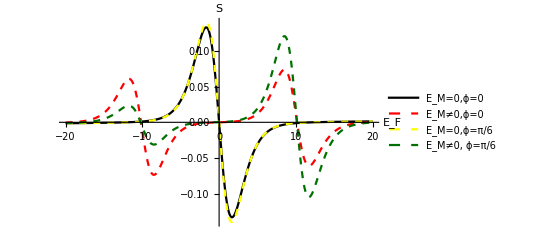

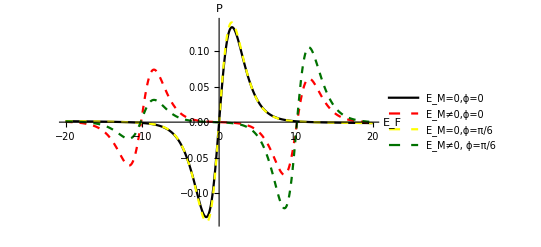

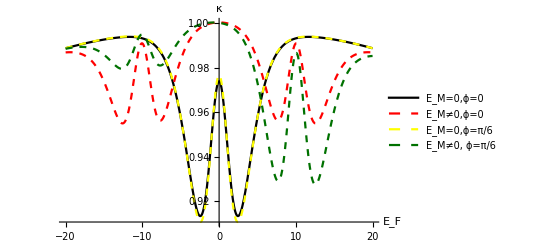

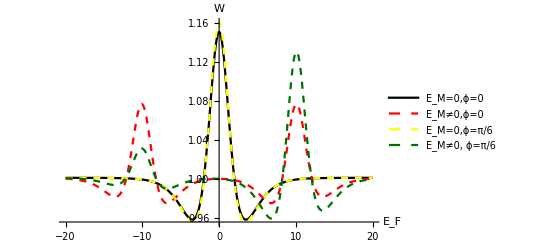

```mathematica
kbT = 1;                (*T = 115mK, E0 and Ef are in units of μeV*)
df[E0_,Ef_] := (ⅇ^((E0-Ef)/kbT)/((1+ⅇ^((E0-Ef)/kbT))^2 kbT));
(*Partial derivative of Fermi function with respect to incident electron energy*)









(*Defining the transmission probability*)

T1[E0_,Ef_,V_,phi_,Em_] :=4 ⅇ^(-Im[E0]/100-2 Im[phi]) Abs[(ⅇ^(3/200 ⅈ (E0+Ef)) (-1-ⅈ E0)+ⅇ^(1/200 ⅈ (3 E0+Ef+400 phi)) (-1-ⅈ E0)+ⅇ^(1/200 ⅈ (E0+3 Ef)) (2-2 ⅈ E0)+ⅇ^(1/200 ⅈ (E0+Ef+400 phi)) (2-2 ⅈ E0)-ⅈ ⅇ^(1/100 ⅈ (E0+Ef)) E0+ⅈ ⅇ^(1/100 ⅈ (2 E0+Ef)) E0-2 ⅈ ⅇ^(1/100 ⅈ (E0+2 Ef)) E0-2 ⅈ ⅇ^((ⅈ E0)/100+2 ⅈ phi) E0-ⅈ ⅇ^(1/100 ⅈ (E0+Ef+200 phi)) E0+ⅈ ⅇ^(1/100 ⅈ (2 E0+Ef+200 phi)) E0+ⅈ ⅇ^(1/200 ⅈ (3 E0+Ef)) (ⅈ+E0)+ⅈ ⅇ^(1/200 ⅈ (3 E0+3 Ef+400 phi)) (ⅈ+E0)+2 ⅇ^((ⅈ E0)/100+ⅈ phi) Em-4 ⅇ^((ⅈ Ef)/100+ⅈ phi) Em+2 ⅇ^(1/100 ⅈ (E0+2 Ef+100 phi)) Em-2 ⅇ^(1/200 ⅈ (E0+Ef+200 phi)) Em+2 ⅇ^(1/200 ⅈ (3 E0+Ef+200 phi)) Em-2 ⅇ^(1/200 ⅈ (E0+3 Ef+200 phi)) Em+2 ⅇ^(1/200 ⅈ (3 E0+3 Ef+200 phi)) Em)/(ⅇ^(1/100 ⅈ (2 E0+Ef))-2 ⅇ^(1/100 ⅈ (2 E0+Ef+200 phi))+ⅇ^(1/100 ⅈ (2 E0+Ef+400 phi))+ⅇ^((ⅈ E0)/100+2 ⅈ phi) (4-8 ⅈ E0)+ⅇ^(1/100 ⅈ (E0+2 Ef+200 phi)) (4-8 ⅈ E0)-8 ⅈ ⅇ^(1/200 ⅈ (3 E0+Ef+400 phi)) E0-8 ⅈ ⅇ^(1/200 ⅈ (3 E0+3 Ef+400 phi)) E0+4 ⅇ^((ⅈ E0)/100+ⅈ phi) Em-4 ⅇ^((ⅈ E0)/100+3 ⅈ phi) Em-4 ⅇ^(1/100 ⅈ (E0+2 Ef+100 phi)) Em+4 ⅇ^(3/200 ⅈ (E0+Ef+200 phi)) Em+4 ⅇ^(1/200 ⅈ (3 E0+Ef+200 phi)) Em-4 ⅇ^(1/200 ⅈ (3 E0+3 Ef+200 phi)) Em+4 ⅇ^(1/100 ⅈ (E0+2 Ef+300 phi)) Em-4 ⅇ^(1/200 ⅈ (3 E0+Ef+600 phi)) Em+8 ⅇ^(1/100 ⅈ (E0+Ef+200 phi)) (1+2 E0^2-2 Em^2)+16 ⅇ^(1/200 ⅈ (E0+Ef+400 phi)) (ⅈ E0+E0^2-Em^2)+16 ⅇ^(1/200 ⅈ (E0+3 Ef+400 phi)) (ⅈ E0+E0^2-Em^2)+16 ⅇ^((ⅈ Ef)/100+2 ⅈ phi) (-1+2 ⅈ E0+E0^2-Em^2))]^2+4 ⅇ^(-1/100 Im[E0+Ef+100 phi]) Abs[(-ⅇ^((ⅈ E0)/100+3 ⅈ phi)+ⅇ^(1/100 ⅈ (2 E0+Ef+300 phi))+ⅇ^(1/100 ⅈ (2 E0+Ef+100 phi)) (-1-2 ⅈ E0)+ⅇ^((ⅈ E0)/100+ⅈ phi) (1-2 ⅈ E0)-4 ⅈ ⅇ^(1/200 ⅈ (3 E0+Ef+200 phi)) E0+ⅇ^((ⅈ E0)/100) Em+ⅇ^(1/100 ⅈ (2 E0+Ef)) Em+2 ⅇ^(1/200 ⅈ (3 E0+Ef)) Em-ⅇ^((ⅈ E0)/100+2 ⅈ phi) Em-4 ⅇ^((ⅈ Ef)/100+2 ⅈ phi) Em-ⅇ^(1/100 ⅈ (2 E0+Ef+200 phi)) Em+4 ⅇ^(1/100 ⅈ (E0+2 Ef+200 phi)) Em-4 ⅇ^(1/200 ⅈ (E0+Ef+400 phi)) Em-2 ⅇ^(1/200 ⅈ (3 E0+Ef+400 phi)) Em+4 ⅇ^(1/200 ⅈ (3 E0+3 Ef+400 phi)) Em+ⅇ^(1/100 ⅈ (E0+Ef+100 phi)) (4+8 E0^2-8 Em^2)+4 ⅇ^(1/100 ⅈ (E0+2 Ef+100 phi)) (E0^2-Em^2)+4 ⅇ^(1/200 ⅈ (3 E0+3 Ef+200 phi)) (-ⅈ E0+E0^2-Em^2)+4 ⅇ^(1/200 ⅈ (E0+Ef+200 phi)) (ⅈ E0+E0^2-Em^2)+8 ⅇ^(1/200 ⅈ (E0+3 Ef+200 phi)) (ⅈ E0+E0^2-Em^2)+4 ⅇ^((ⅈ Ef)/100+ⅈ phi) (-1+2 ⅈ E0+E0^2-Em^2))/(ⅇ^(1/100 ⅈ (2 E0+Ef))-2 ⅇ^(1/100 ⅈ (2 E0+Ef+200 phi))+ⅇ^(1/100 ⅈ (2 E0+Ef+400 phi))+ⅇ^((ⅈ E0)/100+2 ⅈ phi) (4-8 ⅈ E0)+ⅇ^(1/100 ⅈ (E0+2 Ef+200 phi)) (4-8 ⅈ E0)-8 ⅈ ⅇ^(1/200 ⅈ (3 E0+Ef+400 phi)) E0-8 ⅈ ⅇ^(1/200 ⅈ (3 E0+3 Ef+400 phi)) E0+4 ⅇ^((ⅈ E0)/100+ⅈ phi) Em-4 ⅇ^((ⅈ E0)/100+3 ⅈ phi) Em-4 ⅇ^(1/100 ⅈ (E0+2 Ef+100 phi)) Em+4 ⅇ^(3/200 ⅈ (E0+Ef+200 phi)) Em+4 ⅇ^(1/200 ⅈ (3 E0+Ef+200 phi)) Em-4 ⅇ^(1/200 ⅈ (3 E0+3 Ef+200 phi)) Em+4 ⅇ^(1/100 ⅈ (E0+2 Ef+300 phi)) Em-4 ⅇ^(1/200 ⅈ (3 E0+Ef+600 phi)) Em+8 ⅇ^(1/100 ⅈ (E0+Ef+200 phi)) (1+2 E0^2-2 Em^2)+16 ⅇ^(1/200 ⅈ (E0+Ef+400 phi)) (ⅈ E0+E0^2-Em^2)+16 ⅇ^(1/200 ⅈ (E0+3 Ef+400 phi)) (ⅈ E0+E0^2-Em^2)+16 ⅇ^((ⅈ Ef)/100+2 ⅈ phi) (-1+2 ⅈ E0+E0^2-Em^2))]^2





(*Different values of Em in μeV*)
Emaj = 10;


(*Different elements of the Onsager matrix, change last input of transmission probability to change Em*)
LeTt[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ] :=( ((E0 - (Ef))/kbT)^(1)) (T1[(E0),Ef,0,phi,Em])(df[E0/kbT,Ef/kbT])
LeVv[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ] :=( ((E0 - (Ef))/kbT)^(0)) (T1[(E0),Ef,0,phi,Em])(df[E0/kbT,Ef/kbT])
LhVv[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ] :=( ((E0 - (Ef))/kbT)^(1)) (T1[(E0),Ef,0,phi,Em])(df[E0/kbT,Ef/kbT])
LhTt[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ] :=( ((E0 - (Ef))/kbT)^(2)) (T1[(E0),Ef,0,phi,Em])(df[E0/kbT,Ef/kbT])

LeV[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ] := NIntegrate[ LeVv[(E0), fer,Em,phi], {E0, -Infinity, Infinity}]

LeT[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ] := NIntegrate[LeTt[(E0), fer, Em,phi]    , {E0, -Infinity, Infinity}]

LhV[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ] := NIntegrate[LhVv[(E0), fer, Em,phi]        , {E0, -Infinity, Infinity}]

LhT[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ] := NIntegrate[LhTt[(E0), fer, Em,phi]  , {E0, -Infinity, Infinity}]


(*Thermoelectric parameters acquired from the Onsager matrix elements*)
k[fer_, Em_, phi_] :=(1/(2))((LeT[fer, Em, phi])^2/(2*(LeV[fer, Em, phi]*LhT[fer, Em, phi])-(LeT[fer, Em, phi]*LhV[fer, Em, phi])))
p[fer_, Em_, phi_] := (1/(4*1)) * ((LeT[fer, Em, phi])^2)/LeV[fer, Em, phi]
S[fer_, Em_, phi_] := -LeT[fer, Em, phi]/LeV[fer, Em, phi]
kappa[fer_, Em_, phi_] := ((LeV[fer, Em, phi]*LhT[fer, Em, phi] - LhV[fer, Em, phi]*LeT[fer, Em, phi])/ (LeV[fer, Em, phi]))/3.285
P[fer_, Em_, phi_] := (LhV[fer, Em, phi]/LeV[fer, Em, phi])(1)
z0[fer_, Em_, phi_] := Em*11.5*(LeV[fer, Em, phi](S[fer, Em, phi])^2/(kappa[fer, Em, phi]))/(1)
Nmax[fer_, Em_, phi_]:=(Sqrt[z0 [fer, Em, phi] + 1] - 1)/(Sqrt[z0[fer, Em, phi] + 1] + 1)
Pmaxr[fer_, Em_, phi_]:= Sqrt[(LhT[fer, Em, phi])(LeV[fer, Em, phi]*LhT[fer, Em, phi] - LhV[fer, Em, phi]*LeT[fer, Em, phi])/(LeV[fer, Em, phi])]







(*Plotting the functions*)
Plot[{S[fer, 0, 0],S[(fer),Emaj, 0],S[fer, 0, Pi/6],S[(fer),Emaj, Pi/6]}, {fer, -20,20}, AxesLabel->{Text[Style["E_F", FontSize->20]], Text[Style["S", FontSize->20]]}, PlotStyle->{{Black, Thick},{Red, Dashed, Thick},{Yellow, Dashed, Thick}, {Darker[Darker[Green]], Dashed, Thick}}, PlotLegends->{"E_M=0,ϕ=0", "E_M≠0,ϕ=0", "E_M=0,ϕ=π/6", "E_M≠0, ϕ=π/6"},PlotPoints->10,PlotRange->All]
Plot[{P[fer, 0,0],P[(fer),Emaj,0],P[fer, 0,Pi/6],P[(fer),Emaj,Pi/6]}, {fer, -20,20}, AxesLabel->{Text[Style["E_F", FontSize->20]], Text[Style["P", FontSize->20]]}, PlotStyle->{{Black, Thick},{Red, Dashed, Thick},{Yellow, Dashed, Thick}, {Darker[Darker[Green]], Dashed, Thick}}, PlotLegends->{"E_M=0,ϕ=0", "E_M≠0,ϕ=0", "E_M=0,ϕ=π/6", "E_M≠0, ϕ=π/6"}, PlotPoints->10,PlotRange->All]
Plot[{kappa[fer, 0,0], kappa[fer,Emaj,0],kappa[fer, 0,Pi/6], kappa[fer,Emaj,Pi/6]}, {fer, -20,20}, AxesLabel->{Text[Style["E_F", FontSize->20]], Text[Style["κ", FontSize->20]]}, PlotStyle->{{Black, Thick},{Red, Dashed, Thick},{Yellow, Dashed, Thick}, {Darker[Darker[Green]], Dashed, Thick}}, PlotLegends->{"E_M=0,ϕ=0", "E_M≠0,ϕ=0", "E_M=0,ϕ=π/6", "E_M≠0, ϕ=π/6"}, PlotPoints->10, PlotRange->All]

Plot[{kappa[fer, 0, 0]/LeV[fer,0, 0], kappa[fer,Emaj, 0]/LeV[fer, Emaj, 0], kappa[fer, 0, Pi/6]/LeV[fer,0, Pi/6], kappa[fer,Emaj, Pi/6]/LeV[fer, Emaj, Pi/6]}, {fer, -20,20}, AxesLabel->{Text[Style["E_F", FontSize->20]], Text[Style["W", FontSize->20]]}, PlotStyle->{{Black, Thick},{Red, Dashed, Thick},{Yellow, Dashed, Thick}, {Darker[Darker[Green]], Dashed, Thick}}, PlotLegends->{"E_M=0,ϕ=0", "E_M≠0,ϕ=0", "E_M=0,ϕ=π/6", "E_M≠0, ϕ=π/6"}, PlotPoints->10, PlotRange->All]

(*
Plot[{p[phi, 0], p[phi,Emaj], p[phi,Emaj1], p[phi,Emaj2]}, { phi, -20,20}, AxesLabel->{Text[Style["Ef(meV)", FontSize->20]], Text[Style["P_Max", FontSize->20]]},PlotStyle->{{Black, Thick},{Red, Dashed, Thick}, {Orange, Dashed, Thick}, {Yellow,Dashed,Thick}}, PlotPoints->10, PlotRange->All]
Plot[{k[phi, 0], k[phi,Emaj], k[phi,Emaj1], k[phi,Emaj2]},  {phi, -20,20}, AxesLabel->{Text[Style["Ef(meV)", FontSize->20]], Text[Style["η_maxP", FontSize->20]]}, PlotStyle->{{Black, Thick},{Red, Dashed, Thick}, {Orange, Dashed, Thick}, {Yellow,Dashed,Thick}}, PlotPoints->10, PlotRange->All]
Plot[{z0[phi, 0], z0[phi,Emaj], z0[phi,Emaj1], z0[phi,Emaj2]},  {phi, -20,20}, AxesLabel->{Text[Style["Ef(meV)", FontSize->20]], Text[Style["Z_T", FontSize->20]]},PlotStyle->{{Black, Thick},{Red, Dashed, Thick}, {Orange, Dashed, Thick}, {Yellow,Dashed,Thick}}, PlotPoints->10, PlotRange->All]
Plot[{3.26*LeV[phi, 0]/kappa[phi,0], 3.26*LeV[phi,Emaj]/kappa[phi,Emaj],3.26*LeV[phi,Emaj1]/kappa[phi,Emaj1],3.26*LeV[phi,Emaj2]/kappa[phi,Emaj2]}, {phi, -60,60}, AxesLabel->{Text[Style["Ef(meV)", FontSize->20]], Text[Style["L", FontSize->20]]}, PlotStyle->{{Black, Thick},{Red, Dashed, Thick}, {Orange, Dashed, Thick}, {Yellow,Dashed,Thick}},PlotPoints->10, PlotRange->All]
Plot[{Pmaxr[phi, 0], Pmaxr[phi,Emaj],Pmaxr[phi,Emaj1],Pmaxr[phi,Emaj2]},  {phi, -20,20}, AxesLabel->{Text[Style["Ef(meV)", FontSize->20]], Text[Style["P^r", FontSize->20]]}, PlotStyle->{{Black, Thick},{Red, Dashed, Thick}, {Orange, Dashed, Thick}, {Yellow,Dashed,Thick}}, PlotPoints->10, PlotRange->All]
Plot[{kappa[phi, 0], kappa[phi,Emaj],kappa[phi,Emaj1],kappa[phi,Emaj2]}, {phi, -20,20}, AxesLabel->{Text[Style["Ef(meV)", FontSize->20]], Text[Style["κ", FontSize->20]]}, PlotStyle->{{Black, Thick},{Red, Dashed, Thick}, {Orange, Dashed, Thick}, {Yellow,Dashed,Thick}}, PlotPoints->10, PlotRange->All]
Plot[{Nmax[phi, 0], Nmax[phi,Emaj], Nmax[phi,Emaj1], Nmax[phi,Emaj2]},  {phi, -20,20}, AxesLabel->{Text[Style["Ef(meV)", FontSize->20]], Text[Style["P^r", FontSize->20]]}, PlotStyle->{{Black, Thick},{Red, Dashed, Thick}, {Orange, Dashed, Thick}, {Yellow,Dashed,Thick}}, PlotPoints->10, PlotRange->All]
*)
```